# Making graphs for puro

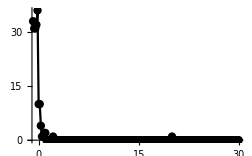
## Old graphing method : -Graphics- NO yellow vs white spots. Just showing # green spots colocalizing with red

```mathematica
{FileNameSetter[Dynamic[mymovie]],Dynamic[mymovie]}
```

{$CellContext`mymovieOpenAll,}

```mathematica
myFile = Import["/Volumes/MINI 1/_PURO/NT TA TL puro counts.xlsx"];
```

```mathematica
myTimes = myFile[[3,1;;All,3]];
myTransSpots = myFile[[3,1;;All,2]];
```

```mathematica
myData = {myTimes,myTransSpots}//Transpose;
```

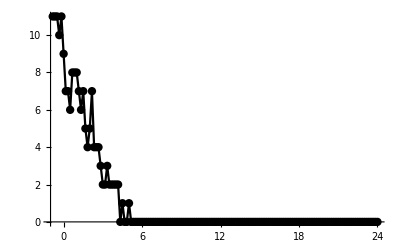

```mathematica
ListPlot[myData, PlotRange->All,Joined->True,AxesOrigin->{-1,0},PlotStyle->Black, Mesh->All]
```

```mathematica
Show[%334,PlotLabel->None,LabelStyle->{FontFamily->"Arial",24,GrayLevel[0]}]
```

-Graphics-

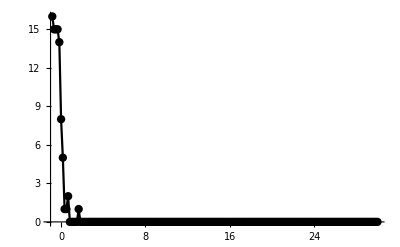

```mathematica
Show[%315,PlotLabel->None,LabelStyle->{FontFamily->"Arial",24,GrayLevel[0]}]
```

```mathematica
Show[%317,PlotLabel->None]
```

-Graphics-

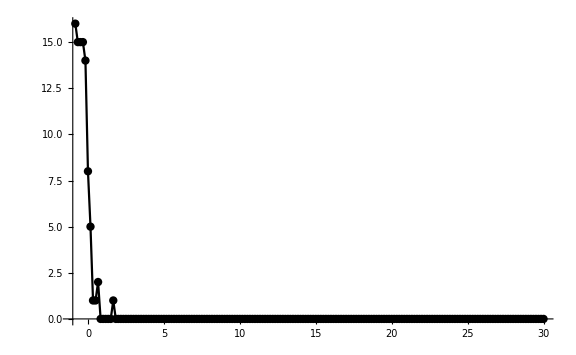

```mathematica
Show[%319,ImageSize->Large]
```

```mathematica
Show[%290,AxesLabel->{HoldForm[Time min],HoldForm[Number of translating RNA]},PlotLabel->None,LabelStyle->{FontFamily->"Arial",24,GrayLevel[0]}]
```

```mathematica
Show[%316,ImageSize->Large]
```

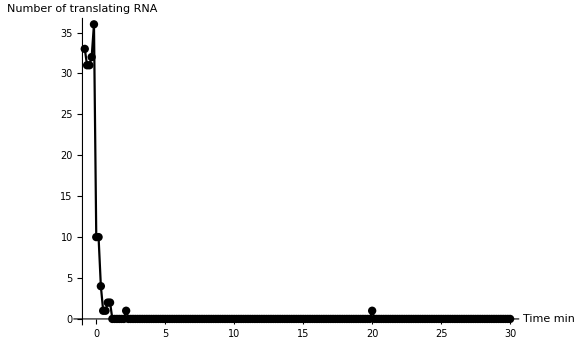

```mathematica
Show[%291,ImageSize->Large]
```

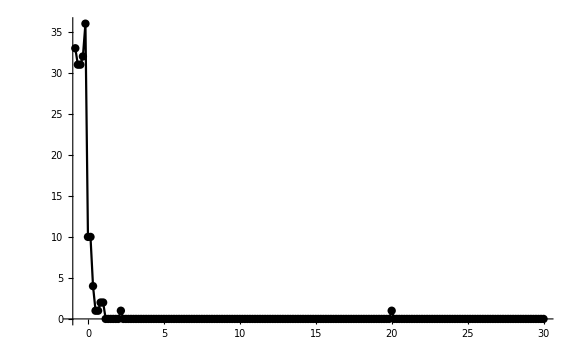

```mathematica
Show[%282,ImageSize->Large, FontSize-> 64]
```

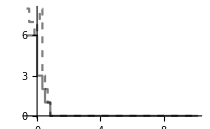
## New style : -Graphics- Survival plot,I reanalyzed these to look at green signal in either white or yellow spots, per cell

#### Parameters :

```mathematica
textfont = LabelStyle->{ FontFamily->"Arial Narrow",32,GrayLevel[.2]};
legend = PlotLegends-> {"Un-tethered, translating mRNA","Tethered, translating mRNA"};
```

#### Data :

Data :    { {yellow spot decay} , {white spot decay} }

```mathematica
excelbook1 = {{"2019 06 22-4","","TA09 Yel","TA09 Wht","TA20 Yel","TA20 Wht","","","","","yel","wt"},{-4.,1.,3.,3.,6.,1.,"","","","","",""},{-3.,2.,3.,3.,6.,1.,"","","","","",""},{-2.,3.,3.,3.,6.,1.,"","","","","",""},{1.,4.,3.,3.,6.,1.,"","","","","",""},{0.,5.,1.,3.,4.,1.,"","","","","",""},{1.,6.,1.,0.,1.,0.,"","","","","",""},{2.,7.,0.,0.,0.,0.,"","","","","",""},{3.,8.,0.,0.,0.,0.,"","","","","",""},{4.,9.,0.,0.,0.,0.,"","","","","",""},{5.,10.,0.,0.,0.,0.,"","","","","",""},{6.,11.,0.,0.,0.,0.,"","","","","",""},{7.,12.,0.,0.,0.,0.,"","","","","",""},{8.,13.,0.,0.,0.,0.,"","","","","",""},{9.,14.,0.,0.,0.,0.,"","","","","",""},{10.,15.,0.,0.,0.,0.,"","","","","",""},{11.,16.,0.,0.,0.,0.,"","","","","",""},{12.,17.,0.,0.,0.,0.,"","","","","",""},{13.,18.,0.,0.,0.,0.,"","","","","",""},{14.,19.,0.,0.,0.,0.,"","","","","",""},{15.,20.,0.,0.,0.,0.,"","","","","",""},{16.,21.,0.,0.,0.,0.,"","","","","",""},{17.,22.,0.,0.,0.,0.,"","","","","",""},{18.,23.,0.,0.,0.,0.,"","","","","",""},{19.,24.,0.,0.,0.,0.,"","","","","",""},{20.,25.,0.,0.,0.,0.,"","","","","",""},{21.,26.,0.,0.,0.,0.,"","","","","",""},{22.,27.,0.,0.,0.,0.,"","","","","",""},{23.,28.,0.,0.,0.,0.,"","","","","",""},{24.,29.,0.,0.,0.,0.,"","","","","",""},{25.,30.,0.,0.,0.,0.,"","","","","",""},{26.,31.,0.,0.,0.,0.,"","","","","",""},{27.,32.,0.,0.,0.,0.,"","","","","",""},{28.,33.,0.,0.,0.,0.,"","","","","",""},{29.,34.,0.,0.,0.,0.,"","","","","",""},{30.,35.,0.,0.,0.,0.,"","","","","",""},{31.,36.,0.,0.,0.,0.,"","","","","",""},{32.,37.,0.,0.,0.,0.,"","","","","",""},{33.,38.,0.,0.,0.,0.,"","","","","",""},{34.,39.,0.,0.,0.,0.,"","","","","",""},{35.,40.,0.,0.,0.,0.,"","","","","",""},{36.,41.,0.,0.,0.,0.,"","","","","",""},{37.,42.,0.,0.,0.,0.,"","","","","",""},{38.,43.,0.,0.,0.,0.,"","","","","",""},{39.,44.,0.,0.,0.,0.,"","","","","",""},{40.,45.,0.,0.,0.,0.,"","","","","",""},{41.,46.,0.,0.,0.,0.,"","","","","",""},{42.,47.,0.,0.,0.,0.,"","","","","",""},{43.,48.,0.,0.,0.,0.,"","","","","",""},{44.,49.,0.,0.,0.,0.,"","","","","",""},{45.,50.,0.,0.,0.,0.,"","","","","",""},{46.,51.,0.,0.,0.,0.,"","","","","",""},{47.,52.,0.,0.,0.,0.,"","","","","",""},{48.,53.,0.,0.,0.,0.,"","","","","",""},{49.,54.,0.,0.,0.,0.,"","","","","",""},{50.,55.,0.,0.,0.,0.,"","","","","",""},{51.,56.,0.,0.,0.,0.,"","","","","",""},{52.,57.,0.,0.,0.,0.,"","","","","",""},{53.,58.,0.,0.,0.,0.,"","","","","",""},{54.,59.,0.,0.,0.,0.,"","","","","",""},{55.,60.,0.,0.,0.,0.,"","","","","",""},{56.,61.,0.,0.,0.,0.,"","","","","",""},{57.,62.,0.,0.,0.,0.,"","","","","",""},{58.,63.,0.,0.,0.,0.,"","","","","",""},{59.,64.,0.,0.,0.,0.,"","","","","",""},{60.,65.,0.,0.,0.,0.,"","","","","",""}} ;
```

```mathematica
excelbook2 =  { {"2019 06 22-4","","","NT02 yel","NT02 Wt","TA02 yel","TA02 wt"},{1.,-40.,-0.6666666666666666,26.,0.,8.,6.},{2.,-30.,-0.5,26.,0.,7.,6.},{3.,-20.,-0.3333333333333333,28.,0.,7.,6.},{4.,-10.,-0.16666666666666666,27.,0.,6.,6.},{5.,0.,0.,27.,0.,7.,3.},{6.,10.,0.16666666666666666,15.,0.,8.,3.},{7.,20.,0.3333333333333333,4.,0.,3.,2.},{8.,30.,0.5,3.,0.,2.,1.},{9.,40.,0.6666666666666666,5.,0.,1.,1.},{10.,50.,0.8333333333333334,2.,0.,0.,0.},{11.,60.,1.,1.,0.,0.,0.},{12.,70.,1.1666666666666667,1.,0.,0.,0.},{13.,80.,1.3333333333333333,2.,0.,0.,0.},{14.,90.,1.5,2.,0.,0.,0.},{15.,100.,1.6666666666666667,2.,0.,0.,0.},{16.,110.,1.8333333333333333,3.,0.,0.,0.},{17.,120.,2.,2.,0.,0.,0.},{18.,130.,2.1666666666666665,1.,0.,0.,0.},{19.,140.,2.3333333333333335,1.,0.,0.,0.},{20.,150.,2.5,1.,0.,0.,0.},{21.,160.,2.6666666666666665,1.,0.,0.,0.},{22.,170.,2.8333333333333335,1.,0.,0.,0.},{23.,180.,3.,1.,0.,0.,0.},{24.,190.,3.1666666666666665,1.,0.,0.,0.},{25.,200.,3.3333333333333335,1.,0.,0.,0.},{26.,210.,3.5,1.,0.,0.,0.},{27.,220.,3.6666666666666665,1.,0.,0.,0.},{28.,230.,3.8333333333333335,1.,0.,0.,0.},{29.,240.,4.,1.,0.,0.,0.},{30.,250.,4.166666666666667,1.,0.,0.,0.},{31.,260.,4.333333333333333,1.,0.,0.,0.},{32.,270.,4.5,1.,0.,0.,0.},{33.,280.,4.666666666666667,1.,0.,0.,0.},{34.,290.,4.833333333333333,1.,0.,0.,0.},{35.,300.,5.,1.,0.,0.,0.},{36.,310.,5.166666666666667,1.,0.,0.,0.},{37.,320.,5.333333333333333,1.,0.,0.,0.},{38.,330.,5.5,1.,0.,0.,0.},{39.,340.,5.666666666666667,1.,0.,0.,0.},{40.,350.,5.833333333333333,1.,0.,0.,0.},{41.,360.,6.,1.,0.,0.,0.},{42.,370.,6.166666666666667,1.,0.,0.,0.},{43.,380.,6.333333333333333,1.,0.,0.,0.},{44.,390.,6.5,1.,0.,0.,0.},{45.,400.,6.666666666666667,0.,0.,0.,0.},{46.,410.,6.833333333333333,0.,0.,0.,0.},{47.,420.,7.,0.,0.,0.,0.},{48.,430.,7.166666666666667,0.,0.,0.,0.},{49.,440.,7.333333333333333,0.,0.,0.,0.},{50.,450.,7.5,0.,0.,0.,0.},{51.,460.,7.666666666666667,0.,0.,0.,0.},{52.,470.,7.833333333333333,0.,0.,0.,0.},{53.,480.,8.,0.,0.,0.,0.},{54.,490.,8.166666666666666,0.,0.,0.,0.},{55.,500.,8.333333333333334,0.,0.,0.,0.},{56.,510.,8.5,0.,0.,0.,0.},{57.,520.,8.666666666666666,0.,0.,0.,0.},{58.,530.,8.833333333333334,0.,0.,0.,0.},{59.,540.,9.,0.,0.,0.,0.},{60.,550.,9.166666666666666,0.,0.,0.,0.},{61.,560.,9.333333333333334,0.,0.,0.,0.},{62.,570.,9.5,0.,0.,0.,0.},{63.,580.,9.666666666666666,0.,0.,0.,0.},{64.,590.,9.833333333333334,0.,0.,0.,0.},{65.,600.,10.,0.,0.,0.,0.}} ;
```

```mathematica
excelbook3 ={{"2019 06 22-4","","","TL01 yel","TL01 Wt","","","","","","","yel","wt"},{1.,-40.,-0.6666666666666666,3.,8.,"","","","","","","",""},{2.,-30.,-0.5,3.,8.,"","","","","","","",""},{3.,-20.,-0.3333333333333333,3.,8.,"","","","","","","",""},{4.,-10.,-0.16666666666666666,3.,8.,"","","","","","","",""},{5.,0.,0.,3.,7.,"","","","","","","",""},{6.,10.,0.16666666666666666,3.,8.,"","","","","","","",""},{7.,20.,0.3333333333333333,2.,7.,"","","","","","","",""},{8.,30.,0.5,2.,7.,"","","","","","","",""},{9.,40.,0.6666666666666666,1.,6.,"","","","","","","",""},{10.,50.,0.8333333333333334,1.,6.,"","","","","","","",""},{11.,60.,1.,1.,5.,"","","","","","","",""},{12.,70.,1.1666666666666667,1.,6.,"","","","","","","",""},{13.,80.,1.3333333333333333,1.,4.,"","","","","","","",""},{14.,90.,1.5,1.,5.,"","","","","","","",""},{15.,100.,1.6666666666666667,1.,5.,"","","","","","","",""},{16.,110.,1.8333333333333333,1.,3.,"","","","","","","",""},{17.,120.,2.,1.,2.,"","","","","","","",""},{18.,130.,2.1666666666666665,2.,3.,"","","","","","","",""},{19.,140.,2.3333333333333335,1.,4.,"","","","","","","",""},{20.,150.,2.5,1.,4.,"","","","","","","",""},{21.,160.,2.6666666666666665,1.,3.,"","","","","","","",""},{22.,170.,2.8333333333333335,1.,3.,"","","","","","","",""},{23.,180.,3.,1.,3.,"","","","","","","",""},{24.,190.,3.1666666666666665,1.,3.,"","","","","","","",""},{25.,200.,3.3333333333333335,1.,3.,"","","","","","","",""},{26.,210.,3.5,2.,2.,"","","","","","","",""},{27.,220.,3.6666666666666665,1.,2.,"","","","","","","",""},{28.,230.,3.8333333333333335,1.,3.,"","","","","","","",""},{29.,240.,4.,1.,2.,"","","","","","","",""},{30.,250.,4.166666666666667,1.,1.,"","","","","","","",""},{31.,260.,4.333333333333333,0.,1.,"","","","","","","",""},{32.,270.,4.5,0.,1.,"","","","","","","",""},{33.,280.,4.666666666666667,0.,1.,"","","","","","","",""},{34.,290.,4.833333333333333,1.,1.,"","","","","","","",""},{35.,300.,5.,0.,0.,"","","","","","","",""},{36.,310.,5.166666666666667,0.,0.,"","","","","","","",""},{37.,320.,5.333333333333333,0.,0.,0.,0.,"","","","","",""},{38.,330.,5.5,0.,0.,0.,0.,"","","","","",""},{39.,340.,5.666666666666667,0.,0.,0.,0.,"","","","","",""},{40.,350.,5.833333333333333,0.,0.,0.,0.,"","","","","",""},{41.,360.,6.,0.,0.,0.,0.,"","","","","",""},{42.,370.,6.166666666666667,0.,0.,0.,0.,"","","","","",""},{43.,380.,6.333333333333333,0.,0.,0.,0.,"","","","","",""},{44.,390.,6.5,0.,0.,0.,0.,"","","","","",""},{45.,400.,6.666666666666667,0.,0.,0.,0.,"","","","","",""},{46.,410.,6.833333333333333,0.,0.,0.,0.,"","","","","",""},{47.,420.,7.,0.,0.,0.,0.,"","","","","",""},{48.,430.,7.166666666666667,0.,0.,0.,0.,"","","","","",""},{49.,440.,7.333333333333333,0.,0.,0.,0.,"","","","","",""},{50.,450.,7.5,0.,0.,0.,0.,"","","","","",""},{51.,460.,7.666666666666667,0.,0.,0.,0.,"","","","","",""},{52.,470.,7.833333333333333,0.,0.,0.,0.,"","","","","",""},{53.,480.,8.,0.,0.,0.,0.,"","","","","",""},{54.,490.,8.166666666666666,0.,0.,0.,0.,"","","","","",""},{55.,500.,8.333333333333334,0.,0.,0.,0.,"","","","","",""},{56.,510.,8.5,0.,0.,0.,0.,"","","","","",""},{57.,520.,8.666666666666666,0.,0.,0.,0.,"","","","","",""},{58.,530.,8.833333333333334,0.,0.,0.,0.,"","","","","",""},{59.,540.,9.,0.,0.,0.,0.,"","","","","",""},{60.,550.,9.166666666666666,0.,0.,0.,0.,"","","","","",""},{61.,560.,9.333333333333334,0.,0.,0.,0.,"","","","","",""},{62.,570.,9.5,0.,0.,0.,0.,"","","","","",""},{63.,580.,9.666666666666666,0.,0.,0.,0.,"","","","","",""},{64.,590.,9.833333333333334,0.,0.,0.,0.,"","","","","",""},{65.,600.,10.,0.,0.,0.,0.,"","","","","",""}};
```

#### Code :

```mathematica
times1 = excelbook1[[2;;All,1]]
times2= excelbook2[[2;;All,3]]
times3= times2;
```

{-4.,-3.,-2.,1.,0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,21.,22.,23.,24.,25.,26.,27.,28.,29.,30.,31.,32.,33.,34.,35.,36.,37.,38.,39.,40.,41.,42.,43.,44.,45.,46.,47.,48.,49.,50.,51.,52.,53.,54.,55.,56.,57.,58.,59.,60.}

{-0.666667,-0.5,-0.333333,-0.166667,0.,0.166667,0.333333,0.5,0.666667,0.833333,1.,1.16667,1.33333,1.5,1.66667,1.83333,2.,2.16667,2.33333,2.5,2.66667,2.83333,3.,3.16667,3.33333,3.5,3.66667,3.83333,4.,4.16667,4.33333,4.5,4.66667,4.83333,5.,5.16667,5.33333,5.5,5.66667,5.83333,6.,6.16667,6.33333,6.5,6.66667,6.83333,7.,7.16667,7.33333,7.5,7.66667,7.83333,8.,8.16667,8.33333,8.5,8.66667,8.83333,9.,9.16667,9.33333,9.5,9.66667,9.83333,10.}

```mathematica
excelbook1[[1,3;;6]]
```

{TA09 Yel,TA09 Wht,TA20 Yel,TA20 Wht}

```mathematica
cellTA09 = excelbook1[[2;;All,3;;4]];
cellTA20 =  excelbook1[[2;;All,5;;6]];
```

```mathematica
Table[ Transpose@ { times1, cellTA09[[All,i]] } , {i,1,2}]
```

{{{-4.,3.},{-3.,3.},{-2.,3.},{1.,3.},{0.,1.},{1.,1.},{2.,0.},{3.,0.},{4.,0.},{5.,0.},{6.,0.},{7.,0.},{8.,0.},{9.,0.},{10.,0.},{11.,0.},{12.,0.},{13.,0.},{14.,0.},{15.,0.},{16.,0.},{17.,0.},{18.,0.},{19.,0.},{20.,0.},{21.,0.},{22.,0.},{23.,0.},{24.,0.},{25.,0.},{26.,0.},{27.,0.},{28.,0.},{29.,0.},{30.,0.},{31.,0.},{32.,0.},{33.,0.},{34.,0.},{35.,0.},{36.,0.},{37.,0.},{38.,0.},{39.,0.},{40.,0.},{41.,0.},{42.,0.},{43.,0.},{44.,0.},{45.,0.},{46.,0.},{47.,0.},{48.,0.},{49.,0.},{50.,0.},{51.,0.},{52.,0.},{53.,0.},{54.,0.},{55.,0.},{56.,0.},{57.,0.},{58.,0.},{59.,0.},{60.,0.}},{{-4.,3.},{-3.,3.},{-2.,3.},{1.,3.},{0.,3.},{1.,0.},{2.,0.},{3.,0.},{4.,0.},{5.,0.},{6.,0.},{7.,0.},{8.,0.},{9.,0.},{10.,0.},{11.,0.},{12.,0.},{13.,0.},{14.,0.},{15.,0.},{16.,0.},{17.,0.},{18.,0.},{19.,0.},{20.,0.},{21.,0.},{22.,0.},{23.,0.},{24.,0.},{25.,0.},{26.,0.},{27.,0.},{28.,0.},{29.,0.},{30.,0.},{31.,0.},{32.,0.},{33.,0.},{34.,0.},{35.,0.},{36.,0.},{37.,0.},{38.,0.},{39.,0.},{40.,0.},{41.,0.},{42.,0.},{43.,0.},{44.,0.},{45.,0.},{46.,0.},{47.,0.},{48.,0.},{49.,0.},{50.,0.},{51.,0.},{52.,0.},{53.,0.},{54.,0.},{55.,0.},{56.,0.},{57.,0.},{58.,0.},{59.,0.},{60.,0.}}}

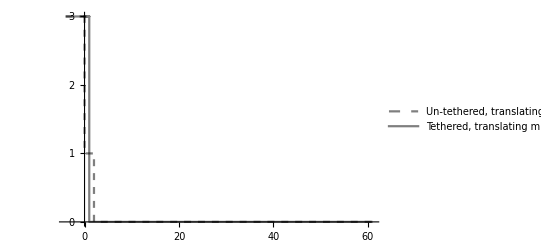

```mathematica
ListStepPlot[Table[ Transpose@ { times1, cellTA09[[All,i]] } , {i,1,2}]  , PlotStyle-> { { Opacity[0.5,Black],Dashed}, Opacity[0.5,Black] }  ,legend , textfont , Ticks-> { Range[0,60,10] , Range[0,3,1] }]
```

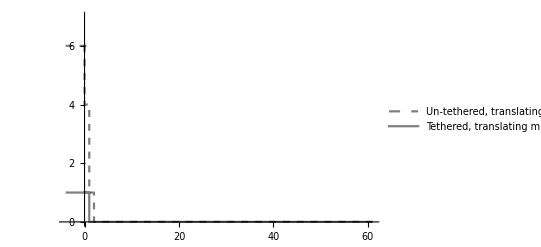

```mathematica
ListStepPlot[Table[ Transpose@ { times1, cellTA20[[All,i]] } , {i,1,2}]  , PlotStyle-> { { Opacity[0.5,Black],Dashed}, Opacity[0.5,Black] }  , legend , textfont , Ticks-> { Range[0,60,10] , Range[0,8,2] } , PlotRange-> {0,7}]
```

```mathematica
cellNT02 = excelbook2[[2;;All,4;;5]]
cellTA02 = excelbook2[[2;;All,6;;7]]
```

{{26.,0.},{26.,0.},{28.,0.},{27.,0.},{27.,0.},{15.,0.},{4.,0.},{3.,0.},{5.,0.},{2.,0.},{1.,0.},{1.,0.},{2.,0.},{2.,0.},{2.,0.},{3.,0.},{2.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{1.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.}}

{{8.,6.},{7.,6.},{7.,6.},{6.,6.},{7.,3.},{8.,3.},{3.,2.},{2.,1.},{1.,1.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.}}

```mathematica
Length@cellNT02
times2
```

65

{-0.666667,-0.5,-0.333333,-0.166667,0.,0.166667,0.333333,0.5,0.666667,0.833333,1.,1.16667,1.33333,1.5,1.66667,1.83333,2.,2.16667,2.33333,2.5,2.66667,2.83333,3.,3.16667,3.33333,3.5,3.66667,3.83333,4.,4.16667,4.33333,4.5,4.66667,4.83333,5.,5.16667,5.33333,5.5,5.66667,5.83333,6.,6.16667,6.33333,6.5,6.66667,6.83333,7.,7.16667,7.33333,7.5,7.66667,7.83333,8.,8.16667,8.33333,8.5,8.66667,8.83333,9.,9.16667,9.33333,9.5,9.66667,9.83333,10.}

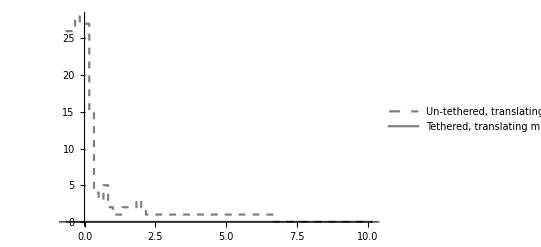

```mathematica
ListStepPlot[Table[ Transpose@ { times2, cellNT02[[All,i]] } , {i,1,2}]  , PlotStyle-> { { Opacity[0.5,Black],Dashed}, Opacity[0.5,Black] }  , PlotRange->All,  
legend , textfont]
```

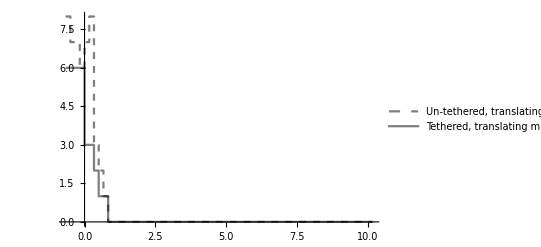

```mathematica
ListStepPlot[Table[ Transpose@ { times2, cellTA02[[All,i]] } , {i,1,2}]  , PlotStyle-> { { Opacity[0.5,Black],Dashed}, Opacity[0.5,Black] }  , PlotRange->All,  legend, textfont]
```

```mathematica
excelbook3[[1 , 4;;5]]
cellTL01 = excelbook3[[2;;All,4;;5]]
Length/@{times3, cellTL01}
```

{TL01 yel,TL01 Wt}

{{3.,8.},{3.,8.},{3.,8.},{3.,8.},{3.,7.},{3.,8.},{2.,7.},{2.,7.},{1.,6.},{1.,6.},{1.,5.},{1.,6.},{1.,4.},{1.,5.},{1.,5.},{1.,3.},{1.,2.},{2.,3.},{1.,4.},{1.,4.},{1.,3.},{1.,3.},{1.,3.},{1.,3.},{1.,3.},{2.,2.},{1.,2.},{1.,3.},{1.,2.},{1.,1.},{0.,1.},{0.,1.},{0.,1.},{1.,1.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.}}

{65,65}

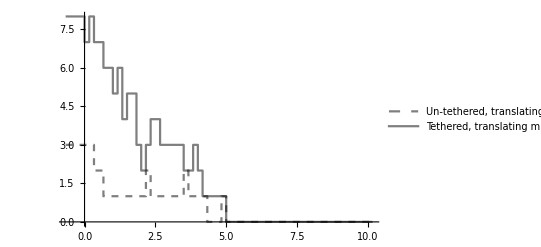

```mathematica
ListStepPlot[Table[ Transpose@ { times3, cellTL01[[All,i]] } , {i,1,2}]  , PlotStyle-> { { Opacity[0.5,Black],Dashed}, Opacity[0.5,Black] }  , PlotRange->All,  legend , textfont]
```